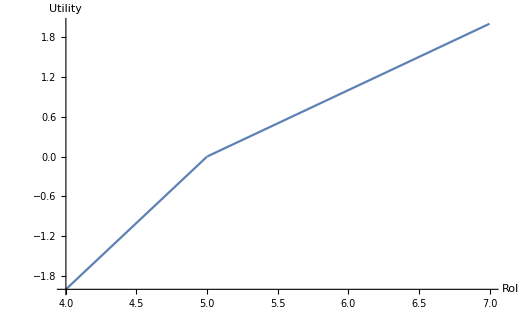

```mathematica
Plot[Max[x-5,0]-2Max[5-x,0],{x,4,7},AxesLabel->{"RoI","Utility"},AxesOrigin->{4,-2},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14}]
```

```mathematica
stocks={"MSFT","AAPL","GOOG"};
y=2015;
```

```mathematica
ans=solveObjective[{"MSFT","AAPL","GOOG"},2015]
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

```mathematica
q=ans
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

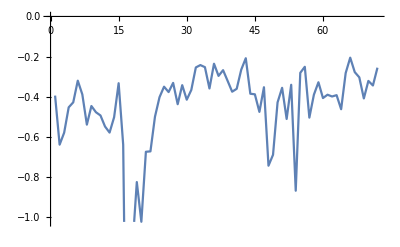

```mathematica
ListLinePlot[xs.ans]
```

```mathematica
rangeVars[q,7]
```

{q$1,q$2,q$3,q$4,q$5,q$6,q$7}

```mathematica
ans=%
```

{q$1→-0.462577,q$2→0.0813624,q$3→0.118456,q$4→0.0476892,q$5→0.0255442,q$6→0.145512,q$7→-0.860971}

```mathematica
rangeVars[q,7]/.ans
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

```mathematica
xs=adjustFeaturesMatrix[x[y]/@stocks];
rs=Flatten[r[y]/@stocks,1];
```

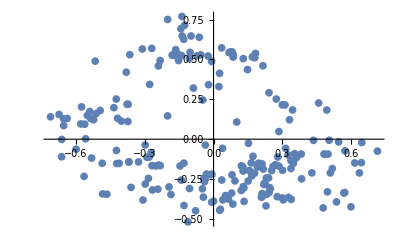

```mathematica
ListPlot@
Flatten[
Map[Function[xStock,
(*#[[3;;4]]&/@xStock]*)
Transpose@MapThread[Standardize[{##},Mean,Function[3StandardDeviation[##]]]&,#[[3;;4]]&/@xStock]],
xs],
1]
```

```mathematica
{a,b,c}≥{1,2,3}
```

{4,b,c}≥{1,2,3}

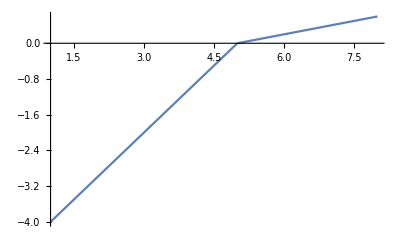

```mathematica
U[p_]:=0.2 (p-5)+Min[(1-0.2)*(p-5),0];
Plot[U[p],{p,1,8}]
```

```mathematica
solveObjective[{"AAPL","GOOG","MSFT","F"},2014]
```

Take::take: Cannot take positions -287 through -1 in {{{2014, 3, 27}, 558.46}, {{2014, 3, 28}, 559.99}, {{2014, 3, 31}, 556.97}, {{2014, 4, 1}, 567.16}, {{2014, 4, 2}, 567.}, {{2014, 4, 3}, 569.74}, {{2014, 4, 4}, 543.14}, « 37 », {{2014, 5, 30}, 559.89}, {{2014, 6, 2}, 553.93}, {{2014, 6, 3}, 544.94}, {{2014, 6, 4}, 544.66}, {{2014, 6, 5}, 553.9}, {{2014, 6, 6}, 556.33}, « 218 »}.

Last::normal: Nonatomic expression expected at position 1 in Last[-287].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{2015, 4, 20}, 535.38}, Last[-287]].

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

Transpose::nmtx: The first two levels of {{{2014, 3, 27}, {2014, 3, 28}, {2014, 3, 31}, {2014, 4, 1}, {2014, 4, 2}, {2014, 4, 3}, {2014, 4, 4}, {2014, 4, 7}, {2014, 4, 8}, {2014, 4, 9}, {2014, 4, 10}, {2014, 4, 11}, {2014, 4, 14}, « 25 », {2014, 5, 21}, {2014, 5, 22}, {2014, 5, 23}, {2014, 5, 27}, {2014, 5, 28}, {2014, 5, 29}, {2014, 5, 30}, {2014, 6, 2}, {2014, 6, 3}, {2014, 6, 4}, {2014, 6, 5}, {2014, 6, 6}, « 218 »}, Take[]} cannot be transposed.

Take::take: Cannot take positions -317 through -1 in {{{2014, 3, 27}, 558.46}, {{2014, 3, 28}, 559.99}, {{2014, 3, 31}, 556.97}, {{2014, 4, 1}, 567.16}, {{2014, 4, 2}, 567.}, {{2014, 4, 3}, 569.74}, {{2014, 4, 4}, 543.14}, « 37 », {{2014, 5, 30}, 559.89}, {{2014, 6, 2}, 553.93}, {{2014, 6, 3}, 544.94}, {{2014, 6, 4}, 544.66}, {{2014, 6, 5}, 553.9}, {{2014, 6, 6}, 556.33}, « 218 »}.

Last::normal: Nonatomic expression expected at position 1 in Last[-317].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{2015, 4, 20}, 535.38}, Last[-317]].

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

Transpose::nmtx: The first two levels of {{{2014, 3, 27}, {2014, 3, 28}, {2014, 3, 31}, {2014, 4, 1}, {2014, 4, 2}, {2014, 4, 3}, {2014, 4, 4}, {2014, 4, 7}, {2014, 4, 8}, {2014, 4, 9}, {2014, 4, 10}, {2014, 4, 11}, {2014, 4, 14}, « 25 », {2014, 5, 21}, {2014, 5, 22}, {2014, 5, 23}, {2014, 5, 27}, {2014, 5, 28}, {2014, 5, 29}, {2014, 5, 30}, {2014, 6, 2}, {2014, 6, 3}, {2014, 6, 4}, {2014, 6, 5}, {2014, 6, 6}, « 218 »}, Take[]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of {{4, 5, 1, 2, 3, 4, 5, 1, 2, 3, 4, 5, 1, 2, 3, 4, 1, 2, 3, 4, 5, 1, 2, 3, 4, 5, 1, 2, 3, 4, 5, 1, 2, 3, 4, 5, 1, 2, 3, 4, 5, 2, 3, 4, 5, 1, 2, 3, 4, 5, « 218 »}, « 4 », {13100, 41100, 10800, 7900, 146700, 5085200, 6351900, 4389600, 3142600, 3321700, 4025800, 3914100, 2568000, « 25 », 1193000, 1611400, 1926900, 2098400, 1647500, 1350400, 1766300, 1431100, 1861500, 1811500, 1684500, 1732000, « 218 »}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose :: argt will be suppressed during this calculation.

$Aborted